```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_r*)
```

```mathematica
nRmin[x_]:=FullSimplify[{-x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_R*)
```

```mathematica
nRmax[x_]:=FullSimplify[{x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
solzpRmin=Solve[nRmin[{Rmin,θ}].{z'[Rmin],0}==ψRmin,z'[Rmin]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{z'[Rmin]→ψRmin/(√(1-ψRmin^2))}

```mathematica
solzpRmax=Solve[nRmin[{Rmax,θ}].{z'[Rmax],0}==ψRmax,z'[Rmax]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{z'[Rmax]→ψRmax/(√(1-ψRmax^2))}

```mathematica
normal[{r,θ}]
```

{-(Cos[θ] z'[r])/(√(1+z'[r]^2)),-(Sin[θ] z'[r])/(√(1+z'[r]^2)),1/(√(1+z'[r]^2))}

```mathematica
(*second fundamental form b*)
```

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

```mathematica
eq=FullSimplify[{κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ H[r]==0},Assumptions->ass]
```

```mathematica
κ=1;
σ=1;
Rmin=1;
Rmax=2;
ϕRmin=1/10;
ϕRmax=0;
ψRmin= 1/2;
ψRmax=0;
```

```mathematica
bcs={z[Rmin]==ϕRmin,z[Rmax]==ϕRmax,z'[Rmin]==(z'[Rmin]/.solzpRmin),z'[Rmax]==(z'[Rmax]/.solzpRmax)};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax}]
```

{{z→InterpolatingFunction[…]}}

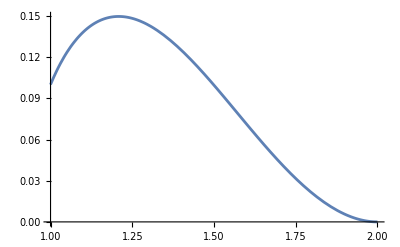

```mathematica
plotex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All]
```

```mathematica
(*sign*)
```

```mathematica
t=Import["~/Desktop/z.csv"];
t=Table[{Sqrt[t[[i,2]]^2+t[[i,3]]^2],t[[i,1]]},{i,1,Length[t]}]
```

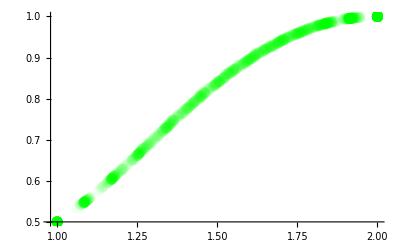

```mathematica
plotnum=ListPlot[t,PlotStyle->{Green,PointSize->0.02, Opacity->0.05},PlotRange->{CC,2 CC}]
```

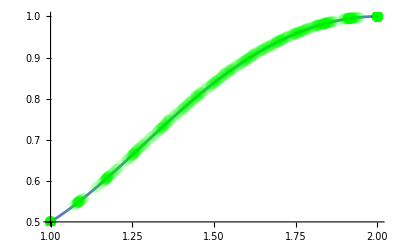

```mathematica
Show[plotex,plotnum]
```

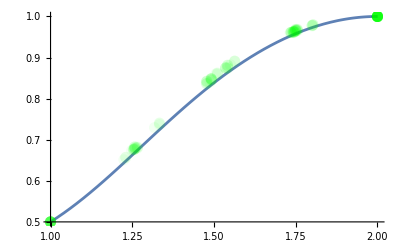

```mathematica
(*r=0.1*)
```

```mathematica
(*r=0.05*)
```